```mathematica
ClearAll["Global`*"]
wd=SetDirectory@NotebookDirectory[];

(* Open Gauss-Legendre Roots and Weights*)

pts=32;
points=pts//ToString;

root=Import[wd<>"/laguerre_"<>points<>"pt.dat"][[All,1]];
weight=Import[wd<>"/laguerre_"<>points<>"pt.dat"][[All,2]];

pTroot[x_]:=x;
pTweight[x_,w_]:=w*Exp[x];

pTTable=Table[{CForm[pTroot[root[[i]]]],CForm[pTweight[root[[i]],weight[[i]]]]},{i,1,Length[root]}];
pTTable=AppendTo[pTTable,""];

Export["pT_gauss_table_"<>points<>"pt.dat",pTTable]
```

pT_gauss_table_32pt.dat

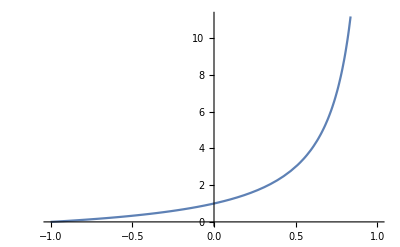

2/(-1+x)^2

```mathematica
Plot[pTroot[x],{x,-1,1}]

D[(1+x)/(1-x),x]//Simplify
```